```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
<<init`
```

## Monochromatic

```mathematica
npeak=16;
nbias=16;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
lapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Mean[lapdata]
```

4.58039×10^-11

```mathematica
Variance[lapdata]
kpeak^4//N
```

0.0242276

0.0237815

```mathematica
dn=2^2;
lap3D=Flatten[Table[{nx,ny,nz,lapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
FigLap3D=ListDensityPlot3D[lap3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
Export["mono_lap_3D.pdf",FigLap3D];
```

```mathematica
Lpeakdata=Import["data/mono_Lpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
Lpeak2D=Flatten[Map[{If[#[[2]]>NL/2,ny=#[[2]]-NL,ny=#[[2]]];If[#[[3]]>NL/2,nz=#[[3]]-NL,nz=#[[3]]];
{ny,nz,#[[4]]}}&,Select[Lpeakdata,#[[1]]==255&]],1]
```

{{53,110,0.265677},{95,-16,0.120924},{104,-71,0.232657},{-124,-113,0.489872},{-111,58,0.266629},{-109,4,0.183461},{-93,72,0.365621},{-90,-122,0.292102},{-89,-121,0.316246},{-82,23,0.27632},{-71,-70,0.303311},{-42,58,0.334987},{-35,39,0.433309},{-25,78,0.290148},{-17,74,0.177023},{-11,50,0.222175},{-9,1,0.352842},{-2,-95,0.258579}}

```mathematica
lap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapdata[[NL^2 255+NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
FigLap2D=Show[ListPlot3D[lap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[Lpeak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Lpeakdata
```

```mathematica
HighLdata=Select[Lpeakdata,#[[4]]>0.5&];
```

```mathematica
Cpeakdata=Import["data/mono_Cpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
HighCdata=Select[Cpeakdata,(#[[5]]>0.3&&#[[1]]<10)&];
```

```mathematica
pairs=Select[Tuples[{HighLdata,HighCdata}],#[[1,{1,2,3}]]==#[[2,{2,3,4}]]&];
```

```mathematica
onlyInL=Select[HighLdata,!MemberQ[HighCdata[[All,{2,3,4}]],#[[{1,2,3}]]]&];
onlyInC=Select[HighCdata,!MemberQ[HighLdata[[All,{1,2,3}]],#[[{2,3,4}]]]&];
```

```mathematica
onlyInC
```

{{6,216,220,21,0.330307}}

```mathematica
dx=20;
onlyInCyz=Flatten[Table[If[ny+216<0,nyt=ny+216+NL,nyt=ny+216];
If[nz+220<0,nzt=nz+220+NL,nzt=nz+220];
{ny,nz,lapdata[[NL^2 6+NL nyt+nzt+1]]},{ny,-dx,dx},{nz,-dx,dx}],1];
onlyInCxz=Flatten[Table[If[nx+6<0,nxt=nx+6+NL,nxt=nx+6];
If[nz+220<0,nzt=nz+220+NL,nzt=nz+220];
{nx,nz,lapdata[[NL^2 nxt+NL 216+nzt+1]]},{nx,-dx,dx},{nz,-dx,dx}],1];
```

```mathematica
FigonlyInCyz=ListPlot3D[onlyInCyz,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
FigonlyInCxz=ListPlot3D[onlyInCxz,PlotRange->Full,AxesLabel->{x,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

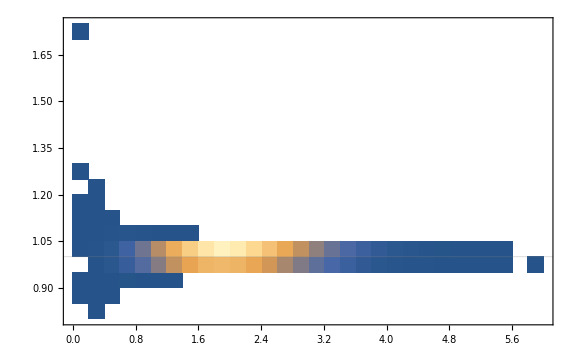

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

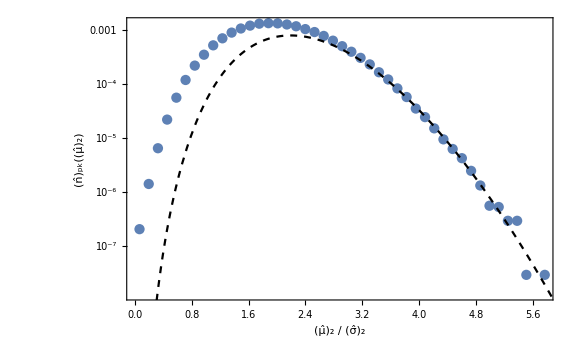

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```